## noise function courtesy of: https://mathematica.stackexchange.com/questions/80486/generating-animations-of-clouds-with-mathematica

```mathematica
lcnoise=With[{perm=Mod[(112 #+185) #+111,256,1]&,mncub=Compile[{{r,_Real}},Which[0≤r<1,16+r^2 (21 r-36),1≤r<2,32+r (-60+(36-7 r) r),True,0]/18,RuntimeAttributes->{Listable}],n=256,vals=RandomReal[{-1,1},256]},Compile[{{x,_Real},{y,_Real},{z,_Real}},Module[{s=0.,fx,fy,fz,ix,iy,iz},ix=Floor[x];iy=Floor[y];iz=Floor[z];
fx=x-ix+1.;fy=y-iy+1.;fz=z-iz+1.;
Do[s+=vals[[Fold[perm[Mod[#1+#2,n,1]]&,0,{iz+k,iy+j,ix+i}]]] mncub[Norm[{i-fx,j-fy,k-fz}]],{i,0,3},{j,0,3},{k,0,3}];s],CompilationOptions->{"InlineCompiledFunctions"->True},RuntimeAttributes->{Listable}]];
```

```mathematica
clouds=Table[DensityPlot[Clip[Sum[lcnoise[2^k x,2^k t,2^k y]/2^k,{k,0,3}],{0,1}],{x,-5,5},{y,-5,5},ColorFunction->(Lighter[RGBColor[0.53,0.81,0.92],#]&),Frame->False],{t,0,5,1/4}];

ListAnimate[clouds]
```

## different approach to noise

```mathematica
n=256;
k2=Outer[Plus,#,#]&[RotateRight[N@Range[-n,n-1,2]/n,n/2]^2];

spectrum=With[{d:=RandomReal[NormalDistribution[],{n,n}]},(1/n) (d+I d)/(0.000001+k2)];
spectrum[[1,1]]*=0;

im[p_]:=Clip[Re[InverseFourier[spectrum Exp[I p]]],{0,∞}]^0.5

p0=p=Sqrt[k2];

Dynamic@Image@im[p0+=p]
```

## Different Geometries to play with

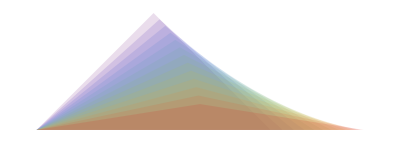

```mathematica
Graphics[{Opacity[0.15],Table[{ColorData["Rainbow"][Rescale[α,{5 π/10,9 π/10}]],SASTriangle[1,α,1]},{α,5 π/10,9 π/10,π/30}]}]
```